## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs6=GenAll[6];Length[baseGraphs6]
```

1

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 6 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations6=CompleteRelations[baseGraphs6];Length[withRelations6]
```

1

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations6[k,"graph"],k],{k,Take[Keys[withRelations6],20]}]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Take::take: Cannot take positions 1 through 20 in Keys[CompleteRelations[GenAll[6]]].

Table::iterb: Iterator {k, Take[Keys[CompleteRelations[GenAll[6]]], 20]} does not have appropriate bounds.

Table[withRelations6[k,graph]k,{k,Take[Keys[CompleteRelations[GenAll[6]]],20]}]

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs6=Select[Reverse[Keys[withRelations6]],CompleteGraphQ[withRelations6[#,"graph"]]&];Length[completeGraphs6]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Keys::argx: Keys called with 0 arguments; 1 argument is expected.

0

```mathematica
baseGraphAxioma6=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->Symbol["v"<>ToString[start]],{k,completeGraphs6}]]
```

Table::iterb: Iterator {k, Keys[]} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table[start++;Symbol[x<>ToString[k]]→Symbol[v<>ToString[start]],{k,Keys[]}]

Now we get some lists of variables

```mathematica
allGraphVariables6=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations6]}];Length[allGraphVariables6]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {key, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

2

```mathematica
baseGraphAxioma6Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma6]]]];Length[baseGraphAxioma6Vars]
```

Table::iterb: Iterator {k, Keys[]} does not have appropriate bounds.

Table::iterb: Iterator {getAllVariables[Keys[]]} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Increment::rvalue: start is not a variable with a value, so its value cannot be changed.

2

```mathematica
baseKeys6=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma6]
```

Table::iterb: Iterator {SymbolToKey[k]} does not have appropriate bounds.

Table[(SymbolToKey[#1⟦1⟧]&)[start++;Symbol[x<>ToString[k]]→Symbol[v<>ToString[start]]],{SymbolToKey[k]}]

```mathematica
Take[baseGraphAxioma6Vars,5]
```

Take::take: Cannot take positions 1 through 5 in Table[{getAllVariables[Keys[]]}, {getAllVariables[vstart]}].

Take[Table[{getAllVariables[Keys[]]},{getAllVariables[vstart]}],5]

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7607 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations6[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma6],
{key,baseKeys6}
],key];
```

Table::iterb: Iterator {key, Table[(SymbolToKey[#1 ⟦ 1 ⟧] &)[start ++; Symbol["x" <> ToString[« 1 »]] → Symbol["v" <> ToString[« 1 »]]], {SymbolToKey[k]}]} does not have appropriate bounds.

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables6=withRelations6;
```

```mathematica
GenerateColorTable6[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[6],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable6[withColorTables6,2]
```

Part::partd: Part specification CompleteRelations[GenAll[6]][2]["matrix"] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification CompleteRelations[GenAll[6]][2]["matrix"] ⟦ 1, 3 ⟧ is longer than depth of object.

Part::partd: Part specification CompleteRelations[GenAll[6]][2]["matrix"] ⟦ 1, 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 2 of CompleteRelations[GenAll[6]][2]["matrix"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{If[CompleteRelations[GenAll[6]][2][matrix]⟦1,2⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦1,3⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦1,4⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦1,5⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦1,6⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦2,3⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦2,4⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦2,5⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦2,6⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦3,4⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦3,5⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦3,6⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦4,5⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦4,6⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]],If[CompleteRelations[GenAll[6]][2][matrix]⟦5,6⟧==2,{colofour,0},If[value==1,{0,colofour},newsym=Symbol[x<>ToString[2]<>y<>ToString[c⟦1⟧]<>z<>ToString[c⟦2⟧]];{newsym,colofour-newsym}]]}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys6=baseKeys6;
```

```mathematica
baseGraphAxioma6Vars
```

Table[{getAllVariables[Keys[]]},{getAllVariables[vstart]}]

```mathematica
Monitor[Table[
withColorTables6[k]["colortable"]=GenerateColorTable6[withColorTables6,k]
,
{k,baseGraphKeys6}
],k];
```

Table::iterb: Iterator {k, Table[(SymbolToKey[#1 ⟦ 1 ⟧] &)[start ++; Symbol["x" <> ToString[« 1 »]] → Symbol["v" <> ToString[« 1 »]]], {SymbolToKey[k]}]} does not have appropriate bounds.

```mathematica
Keys[withColorTables6[1]]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]][1]] is not a valid Association or a list of rules.

Keys[CompleteRelations[GenAll[6]][1]]

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable6[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables6[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables6[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables6[r1],"colortable"],
withColorTables6[r1,"colortable"]=TryComputeColourTable6[r1],
];
If[!KeyExistsQ[withColorTables6[r2],"colortable"],
withColorTables6[r2,"colortable"]=TryComputeColourTable6[r2],

];
withColorTables6[k,"colortable"]=withColorTables6[r1,"colortable"]+withColorTables6[r2,"colortable"];
withColorTables6[k,"colofour"]=withColorTables6[r1,"colofour"]+withColorTables6[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables6[k]["relations"]}
]
];
withColorTables6[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables6[0],"colortable"]
```

KeyExistsQ::invrl: The argument CompleteRelations[GenAll[6]][0] is not a valid Association or a list of rules.

False

```mathematica
Keys[withColorTables6[4782969]]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]][4782969]] is not a valid Association or a list of rules.

Keys[CompleteRelations[GenAll[6]][4782969]]

```mathematica
TryComputeColourTable6[0]
```

KeyExistsQ::invrl: The argument CompleteRelations[GenAll[6]][0] is not a valid Association or a list of rules.

Table::iterb: Iterator {r, CompleteRelations[GenAll[6]][0]["relations"]} does not have appropriate bounds.

CompleteRelations[GenAll[6]][0,colortable]

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables6[k]["colortable2"]=withColorTables6[k]["colortable"]
,
{k,Keys[withColorTables6]}
],k];
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {k, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp6=withColorTables6;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp6[k,"comp"]=GreaterEqual;withRelations6[k,"comp"]="No IH";k,{k,Keys[withComp6]}]//Length
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {k, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

2

```mathematica
CosyPrint6[key_]:=With[
{current=withComp6[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right], result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp6[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp6[k];
If[depth<maxdepth && ! current["marked"],
withComp6[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
RecalculateComp6[r1,depth+1,maxdepth];
RecalculateComp6[r2,depth+1,maxdepth];
withComp6[k,"comp"]= MayBeReassign[k,withComp6[k,"comp"], withComp6[r1,"comp"],withComp6[r2,"comp"]]
];
]
,{r,withComp6[k]["relations"]}
];
];withComp6[k,"comp"]
]
```

```mathematica
MaxDifference[key_]:=Max[Map[Differences,withComp6[key,"vertexsets"]]]
```

```mathematica
SubsequentSet[set_,n_]:=Block[{ok=True,lower=set-1, previous, breaks=0},
If[Length[set]==1,
ok=True,
previous=lower[[1]];
Table[
If[!((v-previous==1)||(v-previous==n-1)),
breaks++;
If[breaks>1,
ok=False
]
];
previous=v
,{v,Rest[lower]}
]
];
ok
]
```

```mathematica
SubsequentSet[{1,4},4]
```

True

```mathematica
VertexSetIsSubSequent[vertexSets_]:=Fold[And,Map[SubsequentSet[#,Length[Flatten[vertexSets]]]&,vertexSets]]
```

```mathematica
VertexSetIsSubSequent[withComp6[14169481,"vertexsets"]]
```

Part::partd: Part specification 14169480 ⟦ 1 ⟧ is longer than depth of object.

Rest::normal: Nonatomic expression expected at position 1 in Rest[14169480].

Table::iterb: Iterator {v, Rest[14169480]} does not have appropriate bounds.

Table::iterb: Iterator {v, "vertexsets"} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

True

```mathematica
withComp6[14169481,"vertexsets"]
```

CompleteRelations[GenAll[6]][14169481,vertexsets]

```mathematica
SubsequentSet[{1,2,3,4,6},6]
```

True

```mathematica
14169481
```

14169481

```mathematica
Table[withComp6[k,"comp"]=Greater;withRelations6[k,"comp"]="IH";k,{k,Select[baseKeys6,VertexSetIsSubSequent[withComp6[#,"vertexsets"]]&]}]
```

Table::iterb: Iterator {v, "vertexsets"} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table[withComp6[k,comp]=Greater;withRelations6[k,comp]=IH;k,{k,Table[(SymbolToKey[#1⟦1⟧]&)[start++;Symbol[x<>ToString[k]]→Symbol[v<>ToString[start]]],{SymbolToKey[k]}]}]

Set of manual values:

```mathematica
Table[withComp6[k,"comp"]=Greater;withRelations6[k,"comp"]="IH";k,{k,{13810649,12734549,9536777,7961786}}]
```

{13810649,12734549,9536777,7961786}

If a base graph is not planar by itself then the  "comp" should be Equal

```mathematica
Table[withComp6[k,"comp"]=Equal;withRelations6[k,"comp"]="Contains K5";k,{k,Select[baseKeys6,!PlanarGraphQ[withComp6[#,"graph"]]&]}]//Length
```

Table::iterb: Iterator {SymbolToKey[k]} does not have appropriate bounds.

Table::iterb: Iterator {k, Table[(SymbolToKey[#1 ⟦ 1 ⟧] &)[start ++; Symbol["x" <> ToString[« 1 »]] → Symbol["v" <> ToString[« 1 »]]], {SymbolToKey[k]}]} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

2

```mathematica
Table[withComp6[k,"marked"]=False;k,{k,Keys[withComp6]}];markCount=0
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {k, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

0

```mathematica
Monitor[RecalculateComp6[0,0,20],markCount]
```

CompleteRelations[GenAll[6]][0,comp]

```mathematica
Select[Keys[withComp6],withComp6[#,"comp"]==Greater&]//Length
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Keys::argx: Keys called with 0 arguments; 1 argument is expected.

0

```mathematica
MaxDifference[12495505]
```

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[12495505].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences["vertexsets"].

CompleteRelations[GenAll[6]][Differences[12495505],Differences[vertexsets]]

```mathematica
Table[CosyPrint6[k],{k,baseKeys6}]
```

Table::iterb: Iterator {k, Table[(SymbolToKey[#1 ⟦ 1 ⟧] &)[start ++; Symbol["x" <> ToString[« 1 »]] → Symbol["v" <> ToString[« 1 »]]], {SymbolToKey[k]}]} does not have appropriate bounds.

Table[CosyPrint6[k],{k,Table[(SymbolToKey[#1⟦1⟧]&)[start++;Symbol[x<>ToString[k]]→Symbol[v<>ToString[start]]],{SymbolToKey[k]}]}]

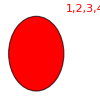
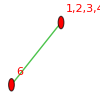
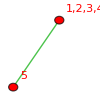
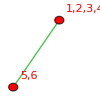
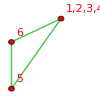
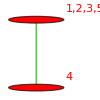
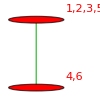
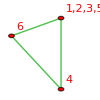
```mathematica
{-Graphics-{14348906->v1,1/6},-Graphics-{14289097->v2,1/2},-Graphics-{->v3,1/2},-Graphics-{14109674->v4,1/2},-Graphics-{14109673->v5,1},-Graphics-{13810649->v6,1/2},-Graphics-{13750846->v7,1/2},-Graphics-{13750843->v8,1},-Graphics-{13631242->v9,1/2},-Graphics-{13631233->v10,1},-Graphics-{13571441->v11,1/2},-Graphics-{13571437->v12,1},-Graphics-{13571431->v13,1},-Graphics-{13571429->v14,1},-Graphics-{13571428->v15,1},-Graphics-{12734549->v16,1/2},-Graphics-{12674794->v17,1/2},-Graphics-{12674767->v18,1},-Graphics-{12555286->v19,1/2},-Graphics-{12555205->v20,1},-Graphics-{12495533->v21,1/2},-Graphics-{12495505->v22,1},-Graphics-{12495451->v23,1},-Graphics-{12495425->v24,1},-Graphics-{12495424->v25,1},-Graphics-{12196778->v26,1/2},-Graphics-{12196535->v27,1},-Graphics-{12137029->v28,1/2},-Graphics-{12136999->v29,1},-Graphics-{12136783->v30,1},-Graphics-{12136759->v31,1},-Graphics-{12136756->v32,1},-Graphics-{12017533->v33,1/2},-Graphics-{12017443->v34,1},-Graphics-{12017281->v35,1},-Graphics-{12017209->v36,1},-Graphics-{12017200->v37,1},-Graphics-{11957786->v38,1/2},-Graphics-{11957755->v39,1},-Graphics-{11957695->v40,1},-Graphics-{11957666->v41,1},-Graphics-{11957665->v42,1},-Graphics-{11957531->v43,1},-Graphics-{11957506->v44,1},-Graphics-{11957503->v45,1},-Graphics-{11957458->v46,1},-Graphics-{11957449->v47,1},-Graphics-{11957435->v48,1},-Graphics-{11957431->v49,1},-Graphics-{11957425->v50,1},-Graphics-{11957423->v51,1},-Graphics-{11957422->v52,0},-Graphics-{9536777->v53,1/2},-Graphics-{9478426->v54,1/2},-Graphics-{9477697->v55,1},-Graphics-{9361726->v56,1/2},-Graphics-{9359539->v57,1},-Graphics-{9303377->v58,1/2},-Graphics-{9302647->v59,1},-Graphics-{9301189->v60,1},-Graphics-{9300461->v61,1},-Graphics-{9300460->v62,1},-Graphics-{9011642->v63,1/2},-Graphics-{9005081->v64,1},-Graphics-{8953297->v65,1/2},-Graphics-{8952565->v66,1},-Graphics-{8946733->v67,1},-Graphics-{8946007->v68,1},-Graphics-{8946004->v69,1},-Graphics-{8836609->v70,1/2},-Graphics-{8834413->v71,1},-Graphics-{8830039->v72,1},-Graphics-{8827861->v73,1},-Graphics-{8827852->v74,1},-Graphics-{8778266->v75,1/2},-Graphics-{8777533->v76,1},-Graphics-{8776069->v77,1},-Graphics-{8775338->v78,1},-Graphics-{8775337->v79,1},-Graphics-{8771693->v80,1},-Graphics-{8770966->v81,1},-Graphics-{8770963->v82,1},-Graphics-{8769514->v83,1},-Graphics-{8769505->v84,1},-Graphics-{8768789->v85,1},-Graphics-{8768785->v86,1},-Graphics-{8768779->v87,1},-Graphics-{8768777->v88,1},-Graphics-{8768776->v89,0},-Graphics-{7961786->v90,1/2},-Graphics-{7942103->v91,1},-Graphics-{7903489->v92,1/2},-Graphics-{7902733->v93,1},-Graphics-{7883779->v94,1},-Graphics-{7883077->v95,1},-Graphics-{7883050->v96,1},-Graphics-{7786897->v97,1/2},-Graphics-{7784629->v98,1},-Graphics-{7767133->v99,1},-Graphics-{7765027->v100,1},-Graphics-{7764946->v101,1},-Graphics-{7728602->v102,1/2},-Graphics-{7727845->v103,1},-Graphics-{7726333->v104,1},-Graphics-{7725578->v105,1},-Graphics-{7725577->v106,1},-Graphics-{7708811->v107,1},-Graphics-{7708108->v108,1},-Graphics-{7708081->v109,1},-Graphics-{7706704->v110,1},-Graphics-{7706623->v111,1},-Graphics-{7706003->v112,1},-Graphics-{7705975->v113,1},-Graphics-{7705921->v114,1},-Graphics-{7705895->v115,1},-Graphics-{7705894->v116,0},-Graphics-{7437137->v117,1/2},-Graphics-{7430333->v118,1},-Graphics-{7417211->v119,1},-Graphics-{7410893->v120,1},-Graphics-{7410650->v121,1},-Graphics-{7378846->v122,1/2},-Graphics-{7378087->v123,1},-Graphics-{7372039->v124,1},-Graphics-{7371286->v125,1},-Graphics-{7371283->v126,1},-Graphics-{7358893->v127,1},-Graphics-{7358188->v128,1},-Graphics-{7358161->v129,1},-Graphics-{7352572->v130,1},-Graphics-{7352329->v131,1},-Graphics-{7351873->v132,1},-Graphics-{7351843->v133,1},-Graphics-{7351627->v134,1},-Graphics-{7351603->v135,1},-Graphics-{7351600->v136,0},-Graphics-{7262266->v137,1/2},-Graphics-{7259989->v138,1},-Graphics-{7255453->v139,1},-Graphics-{7253194->v140,1},-Graphics-{7253185->v141,1},-Graphics-{7242259->v142,1},-Graphics-{7240144->v143,1},-Graphics-{7240063->v144,1},-Graphics-{7235932->v145,1},-Graphics-{7235689->v146,1},-Graphics-{7233835->v147,1},-Graphics-{7233745->v148,1},-Graphics-{7233583->v149,1},-Graphics-{7233511->v150,1},-Graphics-{7233502->v151,0},-Graphics-{7203977->v152,1/2},-Graphics-{7203217->v153,1},-Graphics-{7201699->v154,1},-Graphics-{7200941->v155,1},-Graphics-{7200940->v156,1},-Graphics-{7197161->v157,1},-Graphics-{7196407->v158,1},-Graphics-{7196404->v159,1},-Graphics-{7194901->v160,1},-Graphics-{7194892->v161,1},-Graphics-{7194149->v162,1},-Graphics-{7194145->v163,1},-Graphics-{7194139->v164,1},-Graphics-{7194137->v165,1},-Graphics-{7194136->v166,0},-Graphics-{7183943->v167,1},-Graphics-{7183237->v168,1},-Graphics-{7183210->v169,1},-Graphics-{7181827->v170,1},-Graphics-{7181746->v171,1},-Graphics-{7181123->v172,1},-Graphics-{7181095->v173,1},-Graphics-{7181041->v174,1},-Graphics-{7181015->v175,1},-Graphics-{7181014->v176,0},-Graphics-{7177613->v177,1},-Graphics-{7177370->v178,1},-Graphics-{7176913->v179,1},-Graphics-{7176883->v180,1},-Graphics-{7176667->v181,1},-Graphics-{7176643->v182,1},-Graphics-{7176640->v183,0},-Graphics-{7175515->v184,1},-Graphics-{7175425->v185,1},-Graphics-{7175263->v186,1},-Graphics-{7175191->v187,1},-Graphics-{7175182->v188,0},-Graphics-{7174817->v189,1},-Graphics-{7174786->v190,1},-Graphics-{7174726->v191,1},-Graphics-{7174697->v192,1},-Graphics-{7174696->v193,0},-Graphics-{7174562->v194,1},-Graphics-{7174537->v195,1},-Graphics-{7174534->v196,0},-Graphics-{7174489->v197,1},-Graphics-{7174480->v198,0},-Graphics-{7174466->v199,1},-Graphics-{7174462->v200,0},-Graphics-{7174456->v201,0},-Graphics-{7174454->v202,0},-Graphics-{7174453->v203,0}}
```

```mathematica
Interrupt[]
```

```mathematica
EmbedGraph[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,6,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->6,6<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Monitor[
Table[{key,If[
PlanarGraphQ[EmbedGraph[withComp6,key]],
withComp6[key]["compwhy"]="Embedding is planar and follows IH";withComp6[key]["comp"]=Greater,
withComp6[key]["comp"]=GreaterEqual
]},{key,Keys[withComp6]}],
key];
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {key, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm6=withComp6;
```

```mathematica
Keys[stubbornForm6[1]]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]][1]] is not a valid Association or a list of rules.

Keys[CompleteRelations[GenAll[6]][1]]

```mathematica
CosyPrintThree[key_]:=ColorTablePrint[key,stubbornForm6,"colofour","colortable2"]
```

```mathematica
Table [CosyPrintThree[k],{k,Take[Keys[stubbornForm6],-10]}]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Take::take: Cannot take positions -10 through -1 in Keys[CompleteRelations[GenAll[6]]].

Table::iterb: Iterator {k, Take[Keys[CompleteRelations[GenAll[6]]], -10]} does not have appropriate bounds.

Table[CosyPrintThree[k],{k,Take[Keys[CompleteRelations[GenAll[6]]],-10]}]

```mathematica
ineqsthree=Table[stubbornForm6[k]["comp"][stubbornForm6[k]["colofour"],0],{k,Keys[stubbornForm6]}]//Simplify;
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {k, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

```mathematica
Take[ineqsthree,5]
```

Take::take: Cannot take positions 1 through 5 in Table[stubbornForm6[k]["comp"][stubbornForm6[k]["colofour"], 0], {k, Keys[CompleteRelations[GenAll[6]]]}].

Take[Table[stubbornForm6[k][comp][stubbornForm6[k][colofour],0],{k,Keys[CompleteRelations[GenAll[6]]]}],5]

```mathematica
{v1+v10+v11+v12+v13+v16+v15+v2+v3+v6+v5+v6+v7+v8+v9>0,v10+v12+v13+v15+v2+v3+v5+v7+v8+v9>0,v1+v11+v16+v6+v6>0,v10+v12+v16+v15+v2+v6+v5+v6+v8+v9>0,v10+v12+v15+v2+v5+v8+v9>0}
```

{v1+v10+v11+v12+v13+v15+v16+v2+v3+v5+2 v6+v7+v8+v9>0,v10+v12+v13+v15+v2+v3+v5+v7+v8+v9>0,v1+v11+v16+2 v6>0,v10+v12+v15+v16+v2+v5+2 v6+v8+v9>0,v10+v12+v15+v2+v5+v8+v9>0}

```mathematica
{v1+v2+v6+v6+v5>0,v2+v6+v6>0,v1+v5>0,v2+v6+v5>0,v2+v6>0}
```

{v1+v2+v5+2 v6>0,v2+2 v6>0,v1+v5>0,v2+v5+v6>0,v2+v6>0}

```mathematica
ineqsthree2=Simplify[Fold[And,ineqsthree]];Length[ineqsthree2]
```

3

```mathematica
graphicsthree=Map[stubbornForm6[#,"colofour"]->stubbornForm6[#,"graph"]&,Select[Keys[stubbornForm6],Length[ListofVars[stubbornForm6[#,"colofour"]]]==1&]];TableForm[graphicsthree]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

CompleteRelations[GenAll[6]][CompleteRelations[GenAll[6]],colofour]

```mathematica
graphicsthree2=Map[stubbornForm6[#,"colofour"]->stubbornForm6[#,"graph"]&,Keys[stubbornForm6]];
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

```mathematica
Table [ColorTablePrint[k,stubbornForm6,"colofour","colortable2",Map[#[[1]]->Graph[#[[2]],ImageSize->{60,60}]&,graphicsthree2]],{k,Keys[stubbornForm6]}]
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Table::iterb: Iterator {k, Keys[CompleteRelations[GenAll[6]]]} does not have appropriate bounds.

Table[ColorTablePrint[k,stubbornForm6,colofour,colortable2,(#1⟦1⟧→Graph[#1⟦2⟧,ImageSize→{60,60}]&)/@graphicsthree2],{k,Keys[CompleteRelations[GenAll[6]]]}]

```mathematica
ExpressionToTable2[ineqsthree2]
```

ExpressionToTable2[CompleteRelations[GenAll[6]][k][comp][CompleteRelations[GenAll[6]][k][colofour],0]&&k&&Keys[CompleteRelations[GenAll[6]]]]

```mathematica
{{v1>0}, {v2>0}, {v3>0}, {v6>0}, {v5>0}, {v6>0}, {v7≥0}, {v8≥0}, {v9>0}, {v10>0}, {v11>0}, {v12>0}, {v13≥0}, {v16>0}, {v15≥0}, {v7+v8>0}, {v13+v7>0}, {v15+v8>0}, {v13+v15>0}}
```

{v1>0,v2>0,v3>0,v6>0,v5>0,v6>0,v7≥0,v8≥0,v9>0,v10>0,v11>0,v12>0,v13≥0,v16>0,v15≥0,v7+v8>0,v13+v7>0,v15+v8>0,v13+v15>0}

```mathematica
Style[ExpressionToTable2[ineqsthree2]/.graphicsthree//StandardForm,Large,Bold,Blue]
```

ReplaceAll::reps: {CompleteRelations[GenAll[6]][CompleteRelations[GenAll[6]], "colofour"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ExpressionToTable2[CompleteRelations[GenAll[6]][k][comp][CompleteRelations[GenAll[6]][k][colofour],0]&&k&&Keys[CompleteRelations[GenAll[6]]]]/.CompleteRelations[GenAll[6]][CompleteRelations[GenAll[6]],colofour]

```mathematica
{{-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics-≥0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}}
```

{-Graphics->0,-Graphics->0,-Graphics->0,-Graphics->0,-Graphics->0,-Graphics->0,-Graphics-≥0,-Graphics-≥0,-Graphics->0,-Graphics->0,-Graphics->0,-Graphics->0,-Graphics-≥0,-Graphics->0,-Graphics-≥0,-Graphics-+-Graphics->0,-Graphics-+-Graphics->0,-Graphics-+-Graphics->0,-Graphics-+-Graphics->0}

```mathematica
Map[stubbornForm6[#,"graph"]->Style[StandardForm[stubbornForm6[#,"colofour"]/.graphicsthree],Large,Bold,Blue]&,Select[Keys[stubbornForm6],Length[ListofVars[stubbornForm6[#,"colofour"]]]!=1&]]//TableForm
```

Keys::invrl: The argument Keys[CompleteRelations[GenAll[6]]] is not a valid Association or a list of rules.

Keys::argx: Keys called with 0 arguments; 1 argument is expected.

Keys[]

```mathematica
{{-Graphics-->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}}
```

{-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-,-Graphics-→-Graphics-+-Graphics-}